25

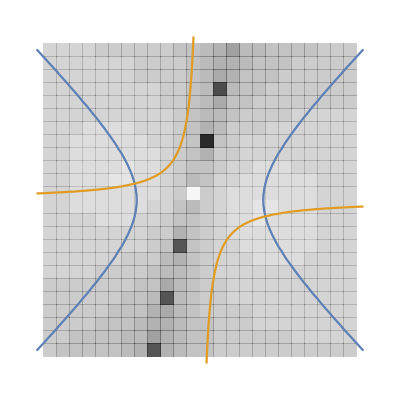

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
iter=ReadList["iter.txt", Number, RecordLists->True];
n=iter[[1]][[1]]
iter=Drop[iter,1];
iter=Partition[ReadList["iter.txt", Number, RecordLists->True]//Flatten,25];
f1=x1^2+x2^2+x1+x2-8;
f2=x1^2+x2^2+x1 x2-7;
f3=x1^2-x2^2-15;
f4=x1 x2+4;
h=20/n;
a=Table[{i,j},{i,-10,10,h},{j,-10,10,h}];
Show[
Graphics[
{Table[
If[iter[[i,j]]>30,
{Red,Rectangle[{a[[i,j,1]]-h/2,a[[i,j,2]]-h/2},{a[[i,j,1]]+h/2,a[[i,j,2]]+h/2}]},
{Opacity[iter[[i,j]]/30],Rectangle[{a[[i,j,1]]-h/2,a[[i,j,2]]-h/2},{a[[i,j,1]]+h/2,a[[i,j,2]]+h/2}]}],{i,2,Length[iter],1},{j,2,Length[iter],1}]}],
ContourPlot[{f3==0,f4==0},{x1,-10,10},{x2,-10,10}]]
```